```mathematica
phi[x_, y_]:=(32*G*thetha*a^2*b^2)/Pi^4 Sum[Sum[(Sin[(i*Pi*x)/a]*Sin[(j*Pi*y)/b])/(i j (b^2 i^2+a^2 j^2)), {i, 1, 10000, 2}],  {j, 1, 21, 2}];
phi[a/2, b/2]/.a->1/.b->1//N
```

0.147355 G thetha

```mathematica
phi2[x_, y_]:=(32*G*thetha*b^2)/Pi^4 Sum[Sum[(Sin[(i*Pi*x)/a]*Sin[(j*Pi*y)/b])/(i j ((b/a)^2 i^2+ j^2)), {i, 1, 200, 2}],  {j, 1, 200, 2}];
phi2[a/2, b/2]/.a->1/.b->1//N
```

0.147343 G thetha

-Graphics3D-

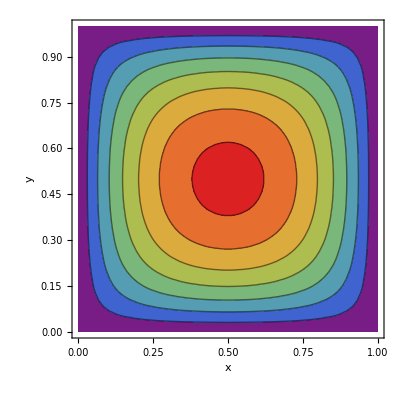

```mathematica
Plot3D[{phi[x, y]/.a->1/.b->1/.thetha->1/.G->1}, {x, 0, 1}, {y, 0, 1},PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, 
           ColorFunction -> "Rainbow", Boxed -> False]
ContourPlot[{phi[x, y]/.a->1/.b->1/.thetha->1/.G->1}, {x, 0, 1}, {y, 0, 1},PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, 
           ColorFunction -> "Rainbow"]
```